```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = Import["/Users/emmanuelflores/GitHub/Tufts/Spring_2025/Computational_Physics/tracker.csv"];
```

```mathematica
timeData = Table[ToExpression[StringSplit[ToString[data[[i]][[1]]]][[1]]],{i,3,62}]-0.764;
```

```mathematica
xData = 0.1*(Table[ToExpression[StringSplit[ToString[data[[i]][[1]]]][[2]]],{i,3,62}]+99.18);
```

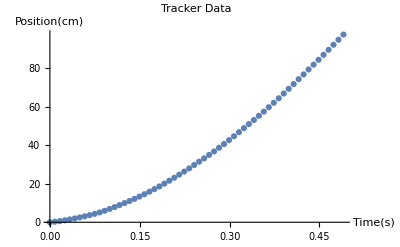

```mathematica
xDataPlot = ListPlot[xData, PlotLabel->"Tracker Data", DataRange->{0, timeData[[-1]]}, AxesLabel->{"Time(s)", "Position(cm)"}]
```

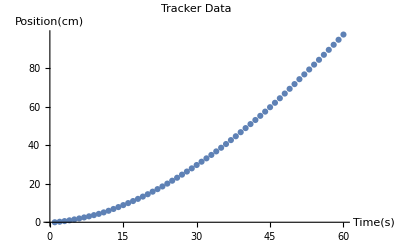

```mathematica
xDataPlotNoScale = ListPlot[xData, PlotLabel->"Tracker Data", AxesLabel->{"Time(s)", "Position(cm)"}]
```

```mathematica
fullData=Transpose[{timeData, xData}]
```

{{0.,0.},{0.009,0.264},{0.017,0.596},{0.025,0.998},{0.034,1.472},{0.042,1.971},{0.05,2.507},{0.058,3.078},{0.067,3.7},{0.075,4.354},{0.083,5.119},{0.092,5.969},{0.1,6.899},{0.108,7.878},{0.117,8.906},{0.125,9.9484},{0.133,11.015},{0.142,12.147},{0.15,13.335},{0.158,14.564},{0.166,15.89},{0.175,17.214},{0.183,18.605},{0.191,20.078},{0.2,21.588},{0.208,23.128},{0.216,24.738},{0.225,26.338},{0.233,27.998},{0.241,29.738},{0.25,31.458},{0.258,33.198},{0.266,34.978},{0.274,36.808},{0.283,38.708},{0.291,40.638},{0.299,42.678},{0.308,44.678},{0.316,46.788},{0.324,48.918},{0.333,50.998},{0.341,53.118},{0.349,55.288},{0.358,57.478},{0.366,59.768},{0.374,62.068},{0.382,64.418},{0.391,66.868},{0.399,69.328},{0.407,71.778},{0.416,74.328},{0.424,76.808},{0.432,79.368},{0.441,81.888},{0.449,84.398},{0.457,86.998},{0.466,89.578},{0.474,92.208},{0.482,94.818},{0.49,97.518}}

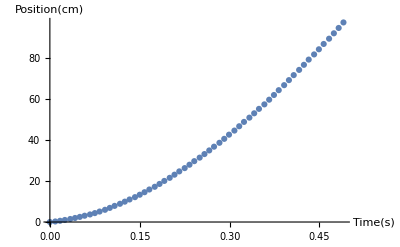

```mathematica
trackerPlot = ListPlot[fullData,AxesLabel->{"Time(s)", "Position(cm)"}]
```

```mathematica
fit =NonlinearModelFit[fullData, x0 + α x+β x^2 ,{x0,α, β},x]
```

FittedModel[…]

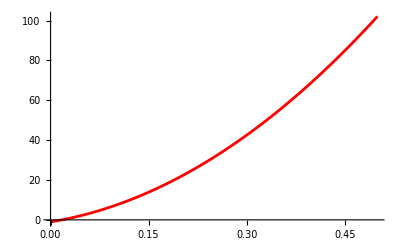

```mathematica
modelPlot = Plot[fit[x],{x,0,0.5}, PlotStyle->Red]
```

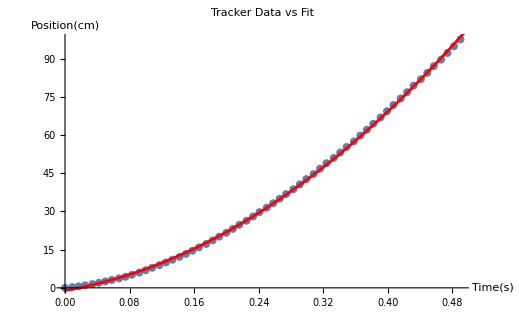

```mathematica
Show[trackerPlot, modelPlot, PlotLegends->{"Tracker Data", "Fit"}, PlotLabel->"Tracker Data vs Fit"]
```